This is the stream plot for 3.16.

3 y'[x]+x y''[x]

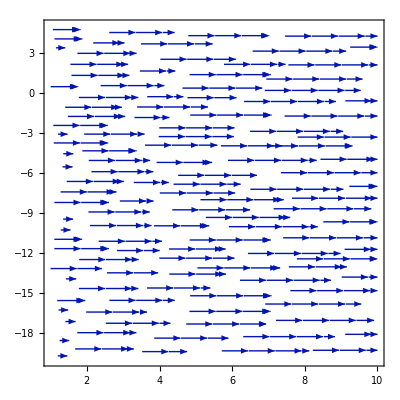

```mathematica
f[x_,y_]=x*y''[x]+3*y'[x]

StreamPlot[{1,f[x,y]},{x,1,10},{y,-20,5}]
```

This is a Runge-Kutta Approximation of the double pendulum. Hooray! This system is extremely chaotic, so a slight change in my initial conditions will produce wildly different results.

```mathematica
m1 = 10
m2 = 7
l1 = 1
l2 = 0.5
g = 9.8
f1 = -(l2/l2)*(m2/(m1+m2))*x2'[t]*Sin[x1[t]-x2[t]]-(g/l1)*Sin[x1[t]]
f2= l1/l2*x1'[t]*Sin[x1[t]-x2[t]]-(g/l2)Sin[x2[t]]
O1=(l2/l1)*(m2/(m1+m2))*Cos[x1[t]-x2[t]]
O2 = l1/l2*Cos[x1[t]-x2[t]]
s=NDSolve[{x1''[t]== f1-O1*f2,x2''[t]==f2-O2*f2,x1'[0]==7,x2'[0]==6, x1[0]==x2[0]==Pi/2},{x1,x2},{t,5},Method->"ExplicitRungeKutta"]
```

10

7

1

0.5

9.8

-9.8 Sin[x1[t]]-0.411765 Sin[x1[t]-x2[t]] x2'[t]

-19.6 Sin[x2[t]]+2. Sin[x1[t]-x2[t]] x1'[t]

0.205882 Cos[x1[t]-x2[t]]

2. Cos[x1[t]-x2[t]]

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

This is a Runge-Kutta Approximation of the spherical pendulum. It is much, much simpler than the double pendulum, and momentum is the phi direction is conserved, which is fun. x is θ and y is ϕ because it makes my life easier.

```mathematica
m = 10
g = 9.8
l = 2
s1 =NDSolve[{y''[t]==-2Tan[x[t]]*y'[t]*x'[t],x''[t]== Sin[x[t]]Cos[x[t]]y'[t]^2-g/1*Sin[x[t]],x'[0]==50,y'[0]==1,x[0]==2,y[0]==1},{x,y},{t,20},Method->"ExplicitRungeKutta"]
```

10

9.8

2

NDSolve::ndstf: At t == 0.0543166, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}